## BDI 513 Final Project - How NVIDIA Drives TSMC

#### Group 8 - Peter Karteczka (peterak2) & Tate Costa (tateec2)

### Defining the Question:

Business problem #1:  (Revenue Concentration Risk): Is TSMC’s financial performance increasingly dependent on NVIDIA’s growth, and does this create a long-term concentration risk? 
Data Questions: 
	- How strongly correlated are TSMC’s and NVIDIA’s revenues over time (quarterly or yearly)?
	- Is NVIDIA’s market cap growth statistically associated with TSMC’s market cap growth?
	- How has the relationship between the two companies changed during the AI boom (e.g., 2020–2024)?

Business problem #2: (Predictability & Co-Movement): If NVIDIA’s product cycle and market performance strongly influence TSMC’s revenue timing and stock movements, can investors and TSMC leadership use NVIDIA’s cycle as an early indicator for TSMC’s future financial performance?”
Data Questions: 
	- How correlated are TSMC and NVIDIA stock returns across different time horizons (daily, monthly, 	yearly)? 
	- Does the correlation between the two stocks increase during major market events? 
	- Do NVIDIA’s stock returns lead TSMC’s returns, indicating predictive power? 
	- Do NVIDIA product launches precede increases in TSMC’s quarterly revenue?

### Getting the Data:

Identifying the data: 
	- Visualization #1: We used the Wolfram FinancialData function to pull the stock data used in this visualization 
	- Visualization #2: 
	- Visualization #3: TSM Locations found from https://www.blackridgeresearch.com/blog/list-of-tsmc-fabs-in-taiwan-arizona-kumamoto?srsltid=AfmBOoon-B5zrnAOu6FvnC6tc2yY8gGoI1MLkS7lKGegVNf78fnF2Uzm . And NVIDIA locations found fromhttps://www.nvidia.com/location-selector/  
Cleaning the data: 
	- Done in visualization code (visualization #3, ...)

### Visualizing Data and Exploring the data

#### Visualization #1 - NVDA & TSM Stock Price Time Series Analysis:

{RGBColor[1, 0, 0],Dashing[{Small,Small}],Line[{{Thu 14 May 2020,0},{Thu 14 May 2020,35000}}]}

{RGBColor[1, 0, 0],Inset[A100 Launch,{Thu 14 May 2020,38000}]}

{RGBColor[1, 0, 0],Dashing[{Small,Small}],Line[{{Tue 22 Mar 2022,0},{Tue 22 Mar 2022,35000}}]}

{RGBColor[1, 0, 0],Inset[H100 Launch,{Wed 2 Mar 2022,38000}]}

{RGBColor[1, 0, 0],Dashing[{Small,Small}],Line[{{Tue 21 Mar 2023,0},{Tue 21 Mar 2023,35000}}]}

{RGBColor[1, 0, 0],Inset[AI Boom,{Tue 21 Mar 2023,38000}]}

TimeSeries[…]

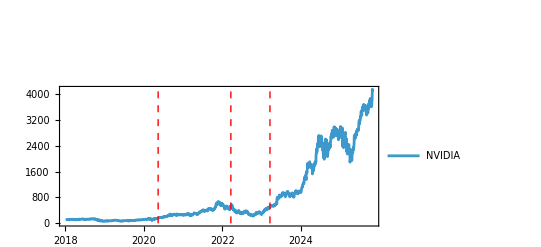

TimeSeries[…]

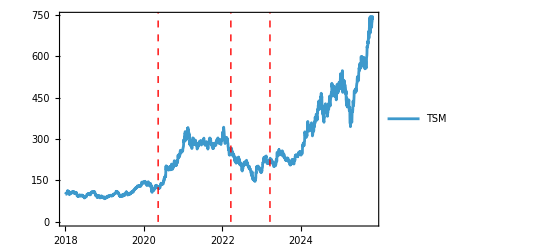

```mathematica
line1 = {Red, Dashed, Line[{{DateObject[{2020,5,14}],0},{DateObject[{2020,5,14}],35000}}]}
label1 = {Red, Inset["A100 Launch", {DateObject[{2020,5,14}],38000}]}
line2 = {Red, Dashed, Line[{{DateObject[{2022,3,22}],0},{DateObject[{2022,3,22}],35000}}]}
label2 = {Red, Inset["H100 Launch", {DateObject[{2022,3,2}],38000}]}
line3 = {Red, Dashed, Line[{{DateObject[{2023,3,21}],0},{DateObject[{2023,3,21}],35000}}]}
label3 = {Red, Inset["AI Boom", {DateObject[{2023,3,21}],38000}]}


Nvidia = FinancialData["NVDA", "CumulativeFractionalChange", {{2018,1,1},{2025,11,1}}]
DateListPlot[{Nvidia}, 
	Epilog-> {line1, label1, line2, label2, line3, label3},
	PlotRange-> All,
	PlotLegends-> 
		Placed[{"NVIDIA"},Above]]

TSM = FinancialData["TSM", "CumulativeFractionalChange", {{2018,1,1},{2025,11,1}}]
DateListPlot[{TSM}, 
	Epilog-> {line1, label1, line2, label2, line3, label3},
	PlotRange-> All,
	PlotLegends-> 
		Placed[{"TSM"},Above]]
```

#### Exploratory Data Analysis

```mathematica
stockReturn=Values[QuantityMagnitude[FinancialData["NVDA","CumulativeFractionalChange",{{2018,1,1},{2025,11,1}}]]];
marketReturn=Values[QuantityMagnitude[FinancialData["TSM","CumulativeFractionalChange",{{2018,1,1},{2025,11,1}}]]];


TableForm[{
{"covariance","correlation"},
{Covariance[stockReturn,marketReturn],
Correlation[stockReturn,marketReturn]}
}]

outcome=Values[QuantityMagnitude[FinancialData["TSM","CumulativeFractionalChange",{{2018,1,1},{2025,11,1}}]]];
predictor1=Values[QuantityMagnitude[FinancialData["NVDA","CumulativeFractionalChange",{{2018,1,1},{2025,11,1}}]]];

dataForRegression1=Transpose[{predictor1,outcome}];
lm1=LinearModelFit[QuantityMagnitude@dataForRegression1,x,x];
Normal[lm1]

lm1["ParameterTable"]

lm1["RSquared"]
```

covariance | correlation
132971. | 0.925722

141.489+0.128724 x

General::munfl: Exp[-1622.11] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1915.52] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
1 | 141.489 | 1.55945 | 90.7299 | 0.
x | 0.128724 | 0.00118608 | 108.529 | 0.

0.856961

About 85% of the variance in the TSMC stock prices can be explained by the changes in stock price in the NVIDIA stock. This demonstrates the deep correlation between the success or failure of TSMC based on the success and failure of NVIDIA.

### Visualization #2 - NVDA & TSMC Quarterly Revenue

### Visualization #3 - Map of TSMC Locations & NVIDIA Cloud AI regions

```mathematica
urlTSM = "https://www.blackridgeresearch.com/blog/list-of-tsmc-fabs-in-taiwan-arizona-kumamoto?srsltid=AfmBOoon-B5zrnAOu6FvnC6tc2yY8gGoI1MLkS7lKGegVNf78fnF2Uzm";
webTSM = Import[urlTSM, "Plaintext"];
countriesTSM = TextCases[webTSM, "Country"];
countriesCleanedTSM = Flatten[StringSplit[countriesTSM, "\n"]];
entitiesTSM = Interpreter["Country"][countriesCleanedTSM];
entitiesCleanedTSM = DeleteDuplicates @ Cases[ReplaceAll[entitiesTSM, Failure[___] -> Nothing], _Entity];
countryCountTSM = Length[entitiesCleanedTSM]
GeoListPlot[entitiesCleanedTSM]
```

5

-Graphics-

```mathematica
urlNVDA = "https://www.nvidia.com/location-selector/";
webNVDA = Import[urlNVDA, "Plaintext"];
countriesNVDA = TextCases[webNVDA, "Country"];
countriesCleanedNVDA = Flatten[StringSplit[countriesNVDA, "\n"]];
entitiesNVDA = Interpreter["Country"][countriesCleanedNVDA];
entitiesCleanedNVDA = DeleteDuplicates @ Cases[ReplaceAll[entitiesNVDA, Failure[___] -> Nothing], _Entity];
countryCountNVDA = Length[entitiesCleanedNVDA]
GeoListPlot[entitiesCleanedNVDA]
```

26

-Graphics-

#### Exploratory Analysis

### Visualization #4 - Executive Background Comparison: TSMC vs NVIDIA

```mathematica
startPattern = "Dr";
TSMceoT=StringJoin[StringSplit[Import["https://www.tsmc.com/english/aboutTSMC/executives", "Plaintext"],"\n"][[{50,51,52}]]];

NVDAceoT= Import["https://nvidianews.nvidia.com/bios/jensen-huang","Plaintext"];

edWord = "degree";
preWORK = "Before|Prior"; 
(*Image*)
NVDAimage= Import["https://nvidianews.nvidia.com/bios/jensen-huang", "Images"][[9]];
TSMimage=Import["https://semiwiki.com/wikis/industry-wikis/dr-c-c-wei-wiki/", "Images"][[10]];
(*Education*)

NVDAed = StringCases[NVDAceoT,
    RegularExpression["[^\\.]*?" <> edWord <> ".*?\\. "]
];

TSMed = StringCases[TSMceoT,
    RegularExpression["[^\\.]*?" <> edWord <> ".*?\\.  "]
];

(*Prior work*)
NVDApre = StringCases[NVDAceoT,
    RegularExpression["[^\\.]*?(" <> preWORK <> ").*?\\."]
];

TSMpre = StringCases[TSMceoT,
    RegularExpression["[^\\.  ]*?(" <> preWORK <> ").*?\\.  "]
];


headerStyle = {Bold};
rowHeaderStyle = {Bold};
imageSize = 120; 

comparisonTable = Grid[{
    (* Column Headers *)
    {Style["Metric", headerStyle], Style["NVIDIA (Jensen Huang)", headerStyle], Style["TSMC (C.C. Wei)", headerStyle]},
    
    (* Row 1: Image *)
    {Style["Photo", rowHeaderStyle], 
        Item[Show[NVDAimage, ImageSize -> imageSize], Alignment -> Center],
        Item[Show[TSMimage, ImageSize -> imageSize], Alignment -> Center]
    },
    
    (* Row 2: Education Background *)
    {Style["Education Background", rowHeaderStyle], 

        Column[NVDAed, Alignment -> Left], 
        Column[TSMed, Alignment -> Left]},
        
    (* Row 3: Prior Career Position *)
    {Style["Before Current Position", rowHeaderStyle], 
        Column[NVDApre, Alignment -> Left], 
        Column[TSMpre, Alignment -> Left]}
    },
    Alignment -> {{Left, Center, Center}, {Automatic}},
    Dividers -> All,
    Spacings -> {1, 1}
];


Print[Style["Executive Background Infographic: NVDA vs TSMC", Bold, 16]];
comparisonTable
```

Executive Background Infographic: NVDA vs TSM

Metric | NVIDIA (Jensen Huang) | TSMC (C.C. Wei)
Photo | -Graphics- | -Graphics-
Education Background |  Morris Chang Exemplary Leadership Award; and honorary doctorate degrees from Taiwan’s National Chiao Tung University, National Taiwan University, and Oregon State University. 
 He holds a BSEE degree from Oregon State University and an MSEE degree from Stanford University.  |  degree in electrical engineering from National Chiao Tung University and Ph.D. from Yale University.  
Before Current Position |   
Prior to founding NVIDIA, Huang worked at LSI Logic and Advanced Micro Devices. | Prior to this appointment, Dr. Wei was TSMC's Chief Executive Officer from June 2018 to June 2024, and TSMC’s Board of Directors elected Dr. Wei as Chairman and Chief Executive Officer in June of 2024. Dr. Wei was President and Co-CEO from November 2013 to June 2018, and Co-Chief Operating Officer from March 2012 to November 2013. From 2009 to 2012, he was TSMC's Senior Vice President of Business Development. Before that, Dr. Wei was Senior Vice President of Mainstream Technology Business.  
Before joining TSMC in 1998, Dr. Wei had served as Senior Vice President of Technology at Chartered Semiconductor and Senior Manager, Logic and SRAM technology development at ST Microelectronics. Prior to that, he was a Member of Technical Staff at Texas Instruments R&D organization.

```mathematica
`
```

### Visualization #5 - Final Infographic